```mathematica
SetDirectory[NotebookDirectory[]];
<<MaTeX`
```

```mathematica
Get["../../lib/lib2.m"];
Get["../../lib/util.m"];
```

```mathematica
SetOptions[MaTeX,"Preamble"->{"\\usepackage{physics,mathtools,newtxtext,newtxmath}"}, FontSize->12];
SetOptions[$FrontEndSession,PrintingStyleEnvironment->"Working"]
texStyle={FontFamily->"Times",FontSize->12};
```

```mathematica
colors=(("DefaultPlotStyle"/. (Method/. Charting`ResolvePlotTheme["Scientific",ListLinePlot]))/. Directive[x_,__]:>x);
```

```mathematica
cm = 72/2.54;
```

```mathematica
plotsDir = "../../../plots/plots-thesis";
If[!DirectoryQ[plotsDir], CreateDirectory[plotsDir]];
```

```mathematica
data = Import["../../../runs/Trials/N9K9/21385198.dat"];
```

```mathematica
changeNK[9, 9];
```

```mathematica
alpha = Import["../../../plots/plots-thesis/7-alpha.dat"];
```

```mathematica
α = alpha[[-1, 2]];
```

```mathematica
randmat = Partition[(# - 1/($N)Tr[#]*IdentityMatrix[$N])&/@RandomVariate[GaussianUnitaryMatrixDistribution[1/(√(α $N)), $N], Length[data]*$K], $K];
```

```mathematica
trX1sqrand = Tr[#[[1]].#[[1]]]&/@randmat//Chop;
```

```mathematica
trX1sq = 1/2#.#&/@data[[All, 2;;($N)^2]];
```

```mathematica
fig[1] = Histogram[{{}, trX1sq}, 350, PDF, 
Frame->True,
FrameStyle->Black,
BaseStyle->texStyle,
PlotTheme->"Scientific",
FrameLabel->MaTeX/@{"\\Tr (X^{1})^2", "\\rho"},
FrameTicks->{{With[{ticks=0+2Range[0,6]//Chop},Thread[{ticks,MaTeX[ticks,"DisplayStyle"->False]}]],None},{With[{ticks=0.1 + 0.2Range[0,8]//Chop},Thread[{ticks,MaTeX[ticks,"DisplayStyle"->False]}]],None}},
ImageSize->14cm,
PlotRange->All
];
```

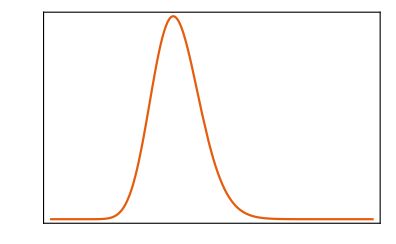

```mathematica
fig[4] = Plot[PDF[GammaDistribution[(($N)^2-1)/2,2/($N α)], x], {x, 0.05, 0.7},
Frame->True,
FrameStyle->Black,
BaseStyle->texStyle,
PlotTheme->"Scientific",
PlotStyle->colors[[1]],
FrameLabel->MaTeX/@{"\\Tr (X^{1})^2", "\\rho"},
FrameTicks->{{With[{ticks=0+2Range[0,6]//Chop},Thread[{ticks,MaTeX[ticks,"DisplayStyle"->False]}]],None},{With[{ticks=0.1 + 0.2Range[0,8]//Chop},Thread[{ticks,MaTeX[ticks,"DisplayStyle"->False]}]],None}},
ImageSize->14cm,
PlotRange->All,
GridLines->None
]
```

```mathematica
plt[1]= Legended[Show[fig[1], fig[4]], Placed[legend, {Bottom, Bottom}]]
```

-Graphics-

```mathematica
Export[plotsDir<>"/9-trX1sq-gue.pdf", plt[1]]
```

../../../plots/plots-thesis/9-trX1sq-gue.pdf

```mathematica
trXsqrand = Sum[Tr[#[[a]].#[[a]]], {a, 1, $K}]&/@randmat//Chop;
```

```mathematica
trXsq = 1/2#.#&/@data[[All, 2;;$K(($N)^2-1)+1]];
```

```mathematica
fig[2] = Histogram[{{}, trXsq}, 350, PDF, 
PlotRange->{{2.0, 3.4}, {0, 3.6}},
Frame->True,
FrameStyle->Black,
BaseStyle->texStyle,
PlotTheme->"Scientific",
FrameLabel->MaTeX/@{"\\Tr X^i X^i", "\\rho"},
FrameTicks->{{With[{ticks=0.5+1.Range[0,6]//Chop},Thread[{ticks,MaTeX[ticks,"DisplayStyle"->False]}]],None},{With[{ticks=2.0 + 0.4Range[0,8]//Chop},Thread[{ticks,MaTeX[ticks,"DisplayStyle"->False]}]],None}},
ImageSize->14cm
];
```

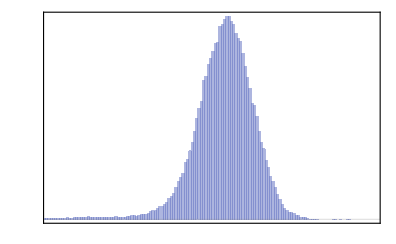

```mathematica
Magnify[fig[2], 1]
```

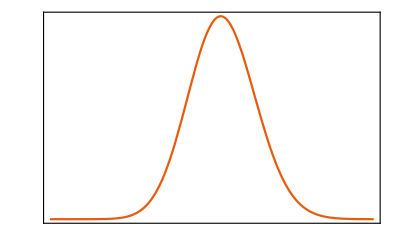

```mathematica
fig[3] = Plot[PDF[GammaDistribution[($K(($N)^2-1))/2,2/($N α)], x], {x, 2, 3.4},
PlotRange->{{2.0, 3.4}, Automatic},
Frame->True,
FrameStyle->Black,
BaseStyle->texStyle,
PlotTheme->"Scientific",
FrameLabel->MaTeX/@{"\\Tr X^i X^i", "\\rho"},
PlotStyle->colors[[1]],
FrameTicks->{{With[{ticks=0.5+1.Range[0,6]//Chop},Thread[{ticks,MaTeX[ticks,"DisplayStyle"->False]}]],None},{With[{ticks=2.0 + 0.4Range[0,8]//Chop},Thread[{ticks,MaTeX[ticks,"DisplayStyle"->False]}]],None}},
ImageSize->14cm,
GridLines->None
]
```

```mathematica
legend = Row[{SwatchLegend[{Opacity[0.5, colors[[2]]]}, {MaTeX@"\\text{simulation}"}], LineLegend[{colors[[1]]}, {MaTeX@"\\text{traceless GUE}"}]}]
```

```mathematica
plt[2]= Legended[Show[fig[2], fig[3]], Placed[legend, {Bottom, Bottom}]]
```

-Graphics-

```mathematica
Export[plotsDir<>"/9-trXsq-gue.pdf", plt[2]]
```

../../../plots/plots-thesis/9-trXsq-gue.pdf

```mathematica
cmatdata = cMatOne/@data;
```

```mathematica
eigrand = Flatten@Map[Eigenvalues, randmat, {2}];
```

```mathematica
eig = Flatten@Map[Eigenvalues, cmatdata[[All, 2;;]], {2}];
```

```mathematica
plt[3] = Histogram[{eig, eigrand}, 350, PDF,
Frame->True,
FrameStyle->Black,
BaseStyle->texStyle,
PlotTheme->"Scientific",
FrameLabel->MaTeX/@{"\\lambda", "\\rho"},
FrameTicks->{{With[{ticks=0.0+0.5Range[0,6]//Chop},Thread[{ticks,MaTeX[ticks,"DisplayStyle"->False]}]],None},{With[{ticks=-0.4 + 0.2Range[0,8]//Chop},Thread[{ticks,MaTeX[ticks,"DisplayStyle"->False]}]],None}},
ChartLegends->Placed[MaTeX/@{"\\text{simulation}", "\\text{traceless GUE}"}, {Bottom, Bottom}],
ImageSize->14cm
];
```

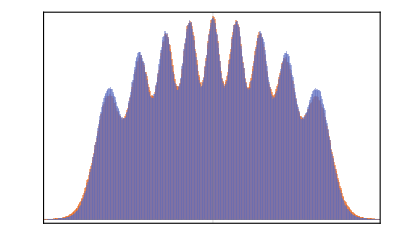

```mathematica
Magnify[plt[3], 1]
```

```mathematica
Export[plotsDir<>"/9-eigenvales-gue.pdf", plt[3]]
```

../../../plots/plots-thesis/9-eigenvales-gue.pdf